## Setup

```mathematica
Get["FunKit`"]
```

Mathematica package TensorBases loaded

Authors: Andreas Geißel, Franz Richard Sattler

Version: 1.0

Year: 2025

For a list of available bases, call TBInfo[]. For further information on a particular basis, call TBInfo["BasisName"].

This package provides the methods TBGetBasisElement, TBGetInnerProduct, TBGetMetric, TBGetInverseMetric, TBGetProjector for every tensor basis available.

For closer explanations, please call their usage messages, e.g. TBGetProjector::usage.

Other useful tools include TBBasisTransformation, TBVertexTransformation, TBGetIdentityMatrix, TBGetBasisSize, TBGetIndexSet, TBMakePropagator.

To build or manipulate bases, please call TBInfo["BaseBuilder"].

To show information on the used notation, call TBInfo["Notation"].

FormTracer package loaded.

To see all (user-defined and package-defined) FormTracer definitions, call TBInfo["FormTracer"].

Furthermore, TensorBases extends FormTracer. To see all extensions, call TBInfo["Extensions"]

To see all momentum transformations that can be performed by TensorBases, call TBInfo["Momenta"].

Lorentz group undefined, using default names.

Group with name color undefined, using default names.

Group with name flavor undefined, using default names.

Welcome to  █▀ ▐▄█ █▚▌ ▐◀ █ ▀█▀
Author: Franz Richard Sattler
Version: 1.1.0
Year: 2025
For more information and a brief introduction to the package, call FInfo[].
To run the testing suite, you can call  FTest[].

Please note for this file, that detailed explanations of any function can be found with Function::usage, e.g.

```mathematica
FTakeDerivatives::usage
```

FTakeDerivatives[setup, expr, derivativeList]
Takes multiple functional derivatives of expr with respect to the fields specified in derivativeList.
Returns the result with all derivative operators resolved.
FTakeDerivatives[setup, expr, derivativeList, "Symmetries" -> symmetries] allows specifying symmetries for simplification.
The derivativeList should be a list of field expressions like {A[i1], A[i2]}.

Also, you can use FInfo[] in any Notebook to get an explanation of some general concepts of FunKit

In the following, we define the gauge-fixed Yang-Mills theory and the truncation used.
First, we define our field space that includes bosonic and fermionic fields A (gluons) and cb,c (ghosts)

```mathematica
fields=<|
"Commuting"-> {A[p,{v, c}]},
"Grassmann"->{{cb[p,{c}],c[p,{c}]}}
|>;
```

Next, the truncation specifies which interactions are taken into account, for each kind of object that can appear in an equation. To see all objects, call ShowIndexedObjects[]. In the following, we set the truncation for fields explicitly to nothing, as we wish to look at the symmetric (vacuum) phase of Yang-Mills theory.

```mathematica
truncation=<|
GammaN->{{A,A},{A,A,A},{A,A,A,A},{A,cb,c},{cb,c}},
Propagator->{{A,A},{cb,c}},Rdot->{{A,A},{cb,c}},
S->{{A,A},{A,A,A},{A,A,A,A},{cb,c},{cb,c,A}},
Field->{{}}
|>;
```

The bases used for explicit tracing of the expressions are specified next. This is used by FunKit to create diagrammatic rules with FMakeDiagrammaticRules[Setup] later on; of course, you can also specify the diagrammatic rules by hand.
If you want to use FMakeDiagrammaticRules, any basis must be known to TensorBases, the framework used by FunKit to manage vertex bases. To see how to define new bases, see both the corresponding publication https://arxiv.org/abs/2503.05580 and the TensorBases showcase notebook at https://github.com/satfra/TensorBases/blob/main/examples/Showcase.nb
To see a list of all available bases, call TBInfo[] and for information on a specific basis TBInfo[“AA”], here at the example of the two-gluon basis.

In the bases Association, we now attach a list of vertex rules to each object that should be written out using TensorBases. There are several ways to specify a basis:
  1. GammaN->{{A, A, A} -> “AAAClass”, ...} simply leads to FunKit using the full basis “AAAClass” for any object GammaN[{A,A,A},{....}]
  2. GammaN->{{A, qb, q} -> {“AqbqDirect”, 1,4,7}, ...} leads to FunKit using the elements 1, 4 and 7 from the basis “AqbqDirect” for any object GammaN[{A,qb,q},{....}]
  3. GammaN->{{A, sb,s} -> {“AqbqDirectSF”, 1,4,7,s->q,sb->qb}, ...} leads to FunKit using the elements 1, 4 and 7 from the basis “AqbqDirectSF” for any object GammaN[{A,sb,s},{....}]
For the third example, the  additional rules are needed to translate the names of fields as used in the basis to the one used in your code.

```mathematica
bases=<|
GammaN->{{A,A}->{"AA",1},{A,A,A}->"AAAClass",{A,A,A,A}->"AAAAClass",{A,cb,c}->{"Acbc",1},{cb,c}->"cbc"},
S->{{A,A}->{"AA",1},{A,A,A}->"AAAClass",{A,A,A,A}->"AAAAClass",{A,cb,c}->{"Acbc",1},{cb,c}->"cbc"},
Propagator->{{A,A}->"AA",{cb,c}->"cbc"},
Rdot->{{A,A}->{"AA",1},{cb,c}->"cbc"}
|>;
```

DiagramStyling does exactly what it sounds like: You can give line-styles for propagators with the associated fields in Feynman diagrams. Note that for paired fields (fermion/antifermion, or complex scalars) you only need to specify one of both.

```mathematica
diagramStyling=<|
"EdgeStyles"->{A->{Orange},c->{Black,Dashed}}
|>;
```

Finally, the setup Association puts the specifics of the theory defined above together and is passed to FunKit as the Global Setup to be used in all calls to FunKit’s functions.
Note that it is not necessary to set a global setup, instead one could also pass Setup as the first parameter to all functions - as this is usually more cumbersome, however, we opt for setting the setup globally.

```mathematica
Setup=<|
"FieldSpace"->fields,
"Truncation"->truncation,
"FeynmanRules"->bases,
"DiagramStyling"->diagramStyling
|>;
FSetGlobalSetup[Setup];
```

Finally, to get correctly formatted LaTeX output, we can add some custom replacements for the FTex and FPrint commands, which we use to actually put a bar above the anti - ghost field instead of printing out cb.

```mathematica
FSetTexStyles[cb->"\\bar{c}"];
```

Using the MakeDiagrammaticRules command, FunKit will produce output where every vertex is dressed with a dressing[Object, {fields, ...}, basisIndex, {momenta, ...}]. We want to explicitly parameterise these dressings with wavefunctions, so we define the function dressingRules in the following:

```mathematica
dressingRules=ReplaceRepeated[#,{
dressing[GammaN,{A,A},1,{p1_,p2_}]:>ZA[√sp[p2,p2]]sp[p2,p2],
dressing[GammaN,{A,A},2,{a_,b_}]:>ξ^-1,
dressing[GammaN,{cb,c},1,{p1_,p2_}]:>-Zc[√sp[p2,p2]]sp[p2,p2],

dressing[InverseProp,{A,A},1,{p1_,p2_}]:>ZA[√sp[p2,p2]]sp[p2,p2],
dressing[InverseProp,{A,A},2,{a_,b_}]:>ξ^-1,
dressing[InverseProp,{cb,c},1,{p1_,p2_}]:>-Zc[√sp[p2,p2]]sp[p2,p2],


dressing[GammaN,{A,cb,c},1,{p1_,p2_,p3_}]:>ZAcbc[p1,p2], 
dressing[GammaN,{A,A,A},1,{p1_,p2_,p3_}]:>ZA3[p1,p2], 
dressing[GammaN,{A,A,A,A},1,{p1_,p2_,p3_,p4_}]:>ZA4[p1,p2,p3] ,

dressing[S,{A,cb,c},1,{p1_,p2_,p3_}]:>gS, 
dressing[S,{A,A,A},1,{p1_,p2_,p3_}]:>gS, 
dressing[S,{A,A,A,A},1,{p1_,p2_,p3_,p4_}]:>gS^2,

dressing[S,{cb,c},1,{p1_,p2_}]->sp[p2,p2],
dressing[S,{A,A},1,{p1_,p2_}]->sp[p2,p2],

ZAcbc[p1_,p2_]:>ZAcbc[√(1/3(sp[p1,p1]+sp[p2,p2]+sp[-p1-p2,-p1-p2]))],
ZA3[p1_,p2_]:>ZA3[√(1/3(sp[p1,p1]+sp[p2,p2]+sp[-p1-p2,-p1-p2]))],
ZA4[p1_,p2_,p3_]:>ZA4[√(1/4(sp[p1,p1]+sp[p2,p2]+sp[p3,p3]+sp[-p1-p2-p3,-p1-p2-p3]))],

nZA->6,
evP:>(k^nZA+1)^(1/nZA),
devP:>k^(-1+nZA) (1+k^nZA)^(-1+1/nZA),
dressing[Rdot,{A,A},1,{p1_,p2_}]:>ZA[evP]RBdot[k^2,sp[p2,p2]]+RB[k^2,sp[p2,p2]](dtZA[evP]+k*devP*((ZA[1.02evP]-ZA[evP])/(0.02*evP))),
dressing[Rdot,{c,cb},1,{p1_,p2_}]:>Zc[k]RBdot[k^2,sp[p2,p2]]+RB[k^2,sp[p2,p2]](dtZc[k]+k((Zc[1.02*k]-Zc[k])/(0.02*k)))
}]&;
```

The FormTracer output contains certain functions for expressing scalar products, which we also convert to explicit variables.

```mathematica
PropParam[expr_]:=UseLorentzLinearity[expr]//.{
lf1->l1,(*FunKit marks purely fermionic loop momenta with an f. This is useful for finite T calculations, where Matsubara frequencies are shifted by πT!*)
sp[p1,p1]->p^2,sp[l2,l2]->l2^2,sp[l1,l1]->l1^2,sp[l1,p1]->l1 p cos[p,l1],sp[l2,p1]->l2 p cos[p,l2],sp[l1,l2]->l1 l2 cos[l1,l2],√(a_^2):>a,(a_^2)^(n_/2):>a^n,
cos[p,l1]:>cospl1,cos[p,l1]:>cospl2
};
SPParam[expr_]:=UseLorentzLinearity[expr]//.{
lf1->l1,(*FunKit marks purely fermionic loop momenta with an f. This is useful for finite T calculations, where Matsubara frequencies are shifted by πT!*)
sp[p,p]->p^2,sp[l1,l1]->l1^2,sp[l1,l2]->l1 l2 cos[l1,l2],
sp[p,l1]->l1 p cos[p,l2],
√(a_^2):>a,(a_^2)^(n_/2):>a^n,(a_^2)^(n_/2):>a^n,Power[Power[l1_,2],Rational[n_,2]]:>l1^n,
cos[p1,l1]:>cosl1p1,cos[p2,l1]:>cosl1p2,cos[p3,l1]:>cosl1p3,cos[p4,l1]:>cosl1p4
};
```

Finally, we just define a few projectors onto symmetric points and set the number of colours to 3.

```mathematica
SP3Project=TBProjectToSymmetricPoint[#,l1,p,p1,p2,p3]&;
SP4Project=TBProjectToSymmetricPoint[#,l1,p,p1,p2,p3,p4]&;
SetNc[3]
$Assumptions=k>0&&p>0&&l1>0&&-1<cos1<1-1<cos2<1&&-1<cos3<1;
```

## DSE

## 2-Point

As a first example, let' s derive the gluon' s gap equation . We create the DSE for the gluon using MakeDSE[A[i1]] (although we could also implement this by hand, it is given for convenience by FunKit).
Note that the output is not yet truncated: Instead of explicit fields (A,cb,c) there are still AnyField in many places.

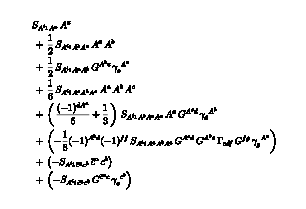

FEx[FTerm[S[{A,A},{-i1,-ci304}],A[ci304]],FTerm[1/2,S[{A,A,A},{-i1,-ci306,-ci305}],A[ci305],A[ci306]],FTerm[1/2,S[{A,A,A},{-i1,-ci307,-ci308}],Propagator[{A,AnyField},{ci308,ci309}],γ[{AnyField,A},{-ci309,ci307}]],FTerm[1/6,S[{A,A,A,A},{-i1,-ci312,-ci311,-ci310}],A[ci310],A[ci311],A[ci312]],FTerm[1/3+1/6 FMinus[{AnyField,A},{ci316,ci313}],S[{A,A,A,A},{-i1,-ci314,-ci315,-ci313}],A[ci313],Propagator[{A,AnyField},{ci315,ci316}],γ[{AnyField,A},{-ci316,ci314}]],FTerm[-1/6,S[{A,A,A,A},{-i1,-ci317,-ci318,-ci319}],Propagator[{A,AnyField},{ci319,ci320}],FMinus[{A,AnyField},{ci318,ci320}],FMinus[{AnyField,AnyField},{ci322,ci322}],Propagator[{A,AnyField},{ci318,ci321}],GammaN[{AnyField,AnyField,AnyField},{-ci321,-ci320,-ci322}],Propagator[{AnyField,AnyField},{ci322,ci323}],γ[{AnyField,A},{-ci323,ci317}]],FTerm[-1,S[{A,cb,c},{-i1,-ci324,-ci325}],cb[ci324],c[ci325]],FTerm[-1,S[{A,cb,c},{-i1,-ci326,-ci327}],Propagator[{cb,AnyField},{ci326,ci328}],γ[{AnyField,c},{-ci328,ci327}]]]

```mathematica
dseA = FMakeDSE[A[i1]]//FPrint
```

To obtain the gap equation, we now take another functional derivative of dseA by using the FTakeDerivatives function . We immediately truncate the result, i . e . insert explicit fields and remove all vertices not specified in the truncation list . The result is plotted, the momentum - routed and printed as LATEX.


-Graphics-+-Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

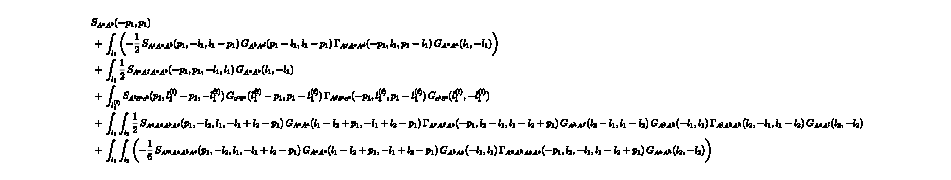

```mathematica
DSEAA=FTakeDerivatives[dseA,{A[i2]}]//FTruncate//FPlot//FRoute//FPrint;
```

The momentum routing returns an association, with the result classified according to the number of loops :

```mathematica
DSEAA//Keys
```

{0-Loop,1-Loop,2-Loop}

The corresponding elements of DSEAA contain the "Expression" itself, a list of "ExternalIndices" and the "LoopMomenta" :

```mathematica
DSEAA["1-Loop"]//Keys
```

{Expression,ExternalIndices,LoopMomenta}

```mathematica
Framed@DSEAA["1-Loop"]["Expression"]
Framed@DSEAA["1-Loop"]["ExternalIndices"]
Framed@DSEAA["1-Loop"]["LoopMomenta"]
```

FEx[FTerm[-1/2,S[{A,A,A},{{p1,{v1,c1}},{-l1,{v398,c399}},{l1-p1,{v401,c402}}}],Propagator[{A,A},{{-l1+p1,{v401,c402}},{l1-p1,{v404,c405}}}],GammaN[{A,A,A},{{-p1,{v2,c2}},{l1,{v407,c408}},{-l1+p1,{v404,c405}}}],Propagator[{A,A},{{l1,{v398,c399}},{-l1,{v407,c408}}}]],FTerm[1/2,S[{A,A,A,A},{{-p1,{v2,c2}},{p1,{v1,c1}},{-l1,{v410,c411}},{l1,{v413,c414}}}],Propagator[{A,A},{{l1,{v410,c411}},{-l1,{v413,c414}}}]],FTerm[S[{A,cb,c},{{p1,{v1,c1}},{lf1-p1,{c458}},{-lf1,{c460}}}],Propagator[{c,cb},{{lf1-p1,{c462}},{-lf1+p1,{c458}}}],GammaN[{A,cb,c},{{-p1,{v2,c2}},{lf1,{c464}},{-lf1+p1,{c462}}}],Propagator[{c,cb},{{lf1,{c460}},{-lf1,{c464}}}]]]

{i1→{p1,{v1,c1}},i2→{-p1,{v2,c2}}}

{l1|lf1}

Next, we project and trace out only the 1-Loop part of the gluon gap equation. You can do the same to the 2-Loop parts, which takes considerably more time.
We use here the function FMakeDiagrammaticRules to create a list of replacement rules for the tensor bases of all vertices, as specified in the setup.

```mathematica
projectorAA=FTerm[TBGetProjector["AA",1,{i1,i2}/.DSEAA["1-Loop"]["ExternalIndices"]]]
```

FTerm[1/24 deltaAdjCol[c1,c2] transProj[-p1,v1,v2]]

```mathematica
DSEAAProjected=projectorAA**DSEAA["1-Loop"]["Expression"]/.FMakeDiagrammaticRules[];
DSEAAResult=FormTrace[DSEAAProjected]//dressingRules//Simplify//PropParam;
```

The Landau gauge result is obtained by taking ξ=0. We could have also done this beforehand - nevertheless, the 1-loop result reads

```mathematica
DSEAAResult/.ξ->0//Simplify//PropParam
```

{(2 (-1+cospl1^2) gS (3 l1^4-6 cospl1 l1^3 p+(8+cospl1^2) l1^2 p^2-6 cospl1 l1 p^3+3 p^4) ZA3[√(2/3) √(l1^2-cospl1 l1 p+p^2)])/(l1^2 (l1^2-2 cospl1 l1 p+p^2)^2 ZA[l1] ZA[√(l1^2-2 cospl1 l1 p+p^2)]),-((-7+cospl1^2) gS^2)/(l1^2 ZA[l1]),-((-1+cospl1^2) gS ZAcbc[√(2/3) √(l1^2-cospl1 l1 p+p^2)])/((l1^2-2 cospl1 l1 p+p^2) Zc[l1] Zc[√(l1^2-2 cospl1 l1 p+p^2)])}

The result can be directly outputted as C++ or Julia code:

```mathematica
MakeCppFunction[Total@DSEAAResult/.ξ->0,"Name"->"DSEAA1Loop","Parameters"->{"l1","p","cospl1","gS","ZA","Zc","ZA3","ZAcbc"}]
MakeJuliaFunction[Total@DSEAAResult/.ξ->0,"Name"->"DSEAA1Loop","Parameters"->{"l1","p","cospl1","gS","ZA","Zc","ZA3","ZAcbc"}]
```

auto DSEAA1Loop(const auto& l1, const auto& p, const auto& cospl1, const auto& gS, const auto& ZA, const auto& Zc, const auto& ZA3, const auto& ZAcbc)
{
  const auto _interp1 = ZA(l1);
  const auto _interp2 = ZA(sqrt(powr<2>(l1) - 2. * cospl1 * l1 * p + powr<2>(p)));
  const auto _interp3 = ZA3(0.816496580927726 * sqrt(powr<2>(l1) - cospl1 * l1 * p + powr<2>(p)));
  const auto _interp4 = ZAcbc(0.816496580927726 * sqrt(powr<2>(l1) - cospl1 * l1 * p + powr<2>(p)));
  const auto _interp5 = Zc(l1);
  const auto _interp6 = Zc(sqrt(powr<2>(l1) - 2. * cospl1 * l1 * p + powr<2>(p)));
  const auto _den1 = powr<-2>(powr<2>(l1) - 2. * cospl1 * l1 * p + powr<2>(p));
  const auto _den2 = powr<-1>(powr<2>(l1) - 2. * cospl1 * l1 * p + powr<2>(p));
  const auto _cse1 = powr<-4>(l1);
  const auto _cse2 = powr<-2>(p);
  const auto _cse3 = -24. * cospl1 * l1 * powr<3>(p);
  const auto _cse4 = powr<-1>(_interp1);
  // clang-format off
  return 0.5 * fma(-32., powr<-1>(_cse2) * _cse4 * _den1 * powr<-1>(_interp2) * _interp3 * gS, fma(-1., _cse2 * _cse3 * _cse4 * _den1 * powr<-1>(_interp2) * _interp3 * gS, fma(2., _den2 * _interp4 * powr<-1>(_interp5) * powr<-1>(_interp6) * gS, fma(-2., _den2 * _interp4 * powr<-1>(_interp5) * powr<-1>(_interp6) * powr<2>(cospl1) * gS, fma(-12., _cse1 * powr<-2>(_cse2) * _cse4 * _den1 * powr<-1>(_interp2) * _interp3 * gS * powr<2>(l1), fma(12., _cse4 * _den1 * powr<-1>(_interp2) * _interp3 * powr<2>(cospl1) * gS * powr<2>(l1), fma(12., _cse1 * powr<-2>(_cse2) * _cse4 * _den1 * powr<-1>(_interp2) * _interp3 * powr<2>(cospl1) * gS * powr<2>(l1), fma(_cse1, _cse3 * _cse4 * _den1 * powr<-1>(_interp2) * _interp3 * powr<2>(cospl1) * gS * powr<2>(l1), fma(14., _cse1 * _cse4 * powr<2>(gS) * powr<2>(l1), fma(-2., _cse1 * _cse4 * powr<2>(cospl1) * powr<2>(gS) * powr<2>(l1), fma(28., _cse1 * powr<-1>(_cse2) * _cse4 * _den1 * powr<-1>(_interp2) * _interp3 * powr<2>(cospl1) * gS * powr<4>(l1), fma(4., _cse1 * powr<-1>(_cse2) * _cse4 * _den1 * powr<-1>(_interp2) * _interp3 * powr<4>(cospl1) * gS * powr<4>(l1), fma(-12., _cse1 * _cse4 * _den1 * powr<-1>(_interp2) * _interp3 * gS * powr<6>(l1), fma(-24., _cse1 * _cse2 * _cse4 * _den1 * powr<-1>(_interp2) * _interp3 * powr<3>(cospl1) * gS * powr<5>(l1) * powr<3>(p), fma(24., _cse1 * _cse2 * _cse4 * _den1 * powr<-1>(_interp2) * _interp3 * cospl1 * gS * powr<3>(l1) * powr<5>(p), 0.)))))))))))))));
  // clang-format on
}

function DSEAA1Loop(l1, p, cospl1, gS, ZA, Zc, ZA3, ZAcbc)
  _interp1 = ZA(l1)
  _interp2 = ZA(sqrt(l1^2 - 2*cospl1*l1*p + p^2))
  _interp3 = ZA3(sqrt(0.6666666666666666)*sqrt(l1^2 - cospl1*l1*p + p^2))
  _interp4 = ZAcbc(sqrt(0.6666666666666666)*sqrt(l1^2 - cospl1*l1*p + p^2))
  _interp5 = Zc(l1)
  _interp6 = Zc(sqrt(l1^2 - 2*cospl1*l1*p + p^2))
  _den1 = (l1^2 - 2*cospl1*l1*p + p^2)^(-2)
  _den2 = 1/(l1^2 - 2*cospl1*l1*p + p^2)
  _cse1 = l1^(-4)
  _cse2 = p^(-2)
  _cse3 = -24*cospl1*l1*p^3
  _cse4 = 1/_interp1
  return fma(-32,(_cse4*_den1*_interp3*gS)/(_cse2*_interp2),fma(-1,(_cse2*_cse3*_cse4*_den1*_interp3*gS)/_interp2,fma(2,(_den2*_interp4*gS)/(_interp5*_interp6),fma(-2,(_den2*_interp4*cospl1^2*gS)/(_interp5*_interp6),fma(-12,(_cse1*_cse4*_den1*_interp3*gS*l1^2)/(_cse2^2*_interp2),fma(12,(_cse4*_den1*_interp3*cospl1^2*gS*l1^2)/_interp2,fma(12,(_cse1*_cse4*_den1*_interp3*cospl1^2*gS*l1^2)/(_cse2^2*_interp2),fma(_cse1,(_cse3*_cse4*_den1*_interp3*cospl1^2*gS*l1^2)/_interp2,fma(14,_cse1*_cse4*gS^2*l1^2,fma(-2,_cse1*_cse4*cospl1^2*gS^2*l1^2,fma(28,(_cse1*_cse4*_den1*_interp3*cospl1^2*gS*l1^4)/(_cse2*_interp2),fma(4,(_cse1*_cse4*_den1*_interp3*cospl1^4*gS*l1^4)/(_cse2*_interp2),fma(-12,(_cse1*_cse4*_den1*_interp3*gS*l1^6)/_interp2,fma(-24,(_cse1*_cse2*_cse4*_den1*_interp3*cospl1^3*gS*l1^5*p^3)/_interp2,fma(24,(_cse1*_cse2*_cse4*_den1*_interp3*cospl1*gS*l1^3*p^5)/_interp2,0)))))))))))))))/2.
end

The same can be of course done for the ghost propagator:

```mathematica
DSEcbc=FTakeDerivatives[FMakeDSE[c[i1]],{cb[i2]}]//FTruncate//FPlot//FRoute//FPrint;
```

-Graphics-+-Graphics-

-Graphics-

## 3Point

Next, we take a look at the ghost - gluon vertex :

```mathematica
DSEAcbc=FTakeDerivatives[FMakeDSE[Setup,c[i1]],{A[i3],cb[i2]}]//FTruncate//FSimplify//FPlot//FRoute//FPrint;
```

-Graphics-+-Graphics-+-Graphics--Graphics-

-Graphics-

This time, we will use a FORM rule to simplify expressions when tracing. For symmetric point projections, FunKit provides methods to make such rules:

```mathematica
Framed@FMakeSPFormRule::usage
SP3FormRule=FMakeSPFormRule[{l1},p,{p1,p2,p3}]
```

FMakeSPFormRule[{l1, l2, ...}, p, {p1, p2, ...}]
Creates a FORM rule for symmetric point momentum configuration.
The first argument is a list of loop momenta {l1, l2, ...}.
The second argument p is the average momentum scale.
The third argument is a list of external leg momenta {p1, p2, ...}.
Projects all momenta to a symmetric configuration with average momentum p.
Crucial for evaluating loop integrals at the symmetric point for RG calculations.

{Vector p1,p2,p3, l1 ,p;
Symbol n;
AutoDeclare CFunction cos;
Set exMom : p1,p2,p3;
Set loopMom : l1;

#define SPOrd "3"

*** project to the SP
#procedure ProjSP()
id FTxsp(p1?exMom,p1?exMom)^-1 = FTxsp(p,p)^-1;
id FTxsp(p1?exMom,p1?exMom) = FTxsp(p,p);
id FTxsp(p1?exMom,p2?exMom)^-1 = (-FTxsp(p,p)/(`SPOrd'-1))^-1;
id FTxsp(p1?exMom,p2?exMom) = -FTxsp(p,p)/(`SPOrd'-1);

id FTxsp(p1?exMom,l1?loopMom)^-1 = (sqrt(FTxsp(p,p))*sqrt(FTxsp(l1,l1))*cos(p1,l1))^-1;
id FTxsp(p1?exMom,l1?loopMom) = (sqrt(FTxsp(p,p))*sqrt(FTxsp(l1,l1))*cos(p1,l1));

#endprocedure

#call SCALL(ProjSP)
.sort}

In the above, SCALL is a predefined routine to recursively apply a method to arguments. Even if you do not understand FORM, you can still use it to project to the symmetric  point when tracing as in the following:

```mathematica
projectorAcbc=FTerm[TBGetProjector["Acbc",1,{i3,i2,i1}/.DSEAcbc["1-Loop"]["ExternalIndices"]]];
DSEAcbcProjected=projectorAcbc**DSEAcbc["1-Loop"]["Expression"]/.FMakeDiagrammaticRules[];
DSEAcbcResult=FormTrace[DSEAcbcProjected,{},SP3FormRule]//dressingRules//SP3Project//SPParam//Simplify;
```

To create C++ code, we would now like to insert some user-defined code to define the angles between the loop momentum l1 and the external momenta p1:

```mathematica
Options["MakeCppFunction"]
```

{Return→auto,Parameters→{},Name→function,Prefix→,Suffix→,CodeParser→Cpp,Body→,Class→,Templates→{},ReturnTransform→Identity}

```mathematica
MakeCppFunction[Total@DSEAcbcResult,
"Name"->"DSEAcbc1Loop",
"Parameters"->{"l1","p","cos1","cos2","gS","ZA","Zc","ZA3","ZAcbc"},
"Body"->"// This is user-defined 
const double cosl1p1 = cos1;
const double cosl1p2 = ((-1.) * (cos1) + (sqrt(3. + (-3.) * (powr<2>(cos1)))) * (cos2)) * (0.5);
const double cosl1p3 = ((-1.) * (cos1) + (-1.) * ((sqrt(3. + (-3.) * (powr<2>(cos1)))) * (cos2))) * (0.5);
// This is not user-defined "
]
```

auto DSEAcbc1Loop(const auto& l1, const auto& p, const auto& cos1, const auto& cos2, const auto& gS, const auto& ZA, const auto& Zc, const auto& ZA3, const auto& ZAcbc)
{
  // This is user-defined
  const double cosl1p1 = cos1;
  const double cosl1p2 = ((-1.) * (cos1) + (sqrt(3. + (-3.) * (powr<2>(cos1)))) * (cos2)) * (0.5);
  const double cosl1p3 = ((-1.) * (cos1) + (-1.) * ((sqrt(3. + (-3.) * (powr<2>(cos1)))) * (cos2))) * (0.5);
  // This is not user-defined
  const auto _interp1 = ZA(l1);
  const auto _interp2 = ZA(sqrt(powr<2>(l1) - 2. * (cosl1p1 + cosl1p2) * l1 * p + powr<2>(p)));
  const auto _interp3 = ZA3(0.816496580927726 * sqrt(powr<2>(l1) - (cosl1p1 + cosl1p2) * l1 * p + powr<2>(p)));
  const auto _interp4 = ZAcbc(sqrt(0.6666666666666666 * powr<2>(l1) - 0.6666666666666666 * (2. * cosl1p1 + cosl1p2) * l1 * p + powr<2>(p)));
  const auto _interp5 = Zc(sqrt(powr<2>(l1) - 2. * cosl1p1 * l1 * p + powr<2>(p)));
  const auto _interp6 = ZAcbc(0.816496580927726 * sqrt(powr<2>(l1) + cosl1p2 * l1 * p + powr<2>(p)));
  const auto _interp7 = ZAcbc(sqrt(0.6666666666666666 * powr<2>(l1) + 0.6666666666666666 * (-cosl1p1 + cosl1p2) * l1 * p + powr<2>(p)));
  const auto _interp8 = Zc(sqrt(powr<2>(l1) + 2. * cosl1p2 * l1 * p + powr<2>(p)));
  const auto _den1 = powr<-1>(powr<2>(l1) - 2. * cosl1p1 * l1 * p + powr<2>(p));
  const auto _den2 = powr<-1>(powr<2>(l1) + 2. * cosl1p2 * l1 * p + powr<2>(p));
  const auto _den3 = powr<-2>(powr<2>(l1) - 2. * (cosl1p1 + cosl1p2) * l1 * p + powr<2>(p));
  const auto _cse1 = powr<-2>(l1);
  const auto _cse2 = powr<-1>(_interp1);
  const auto _cse3 = powr<-1>(_interp5);
  // clang-format off
  return 0.25 * fma(-2., _cse1 * _cse2 * _cse3 * _den1 * _den2 * _interp6 * _interp7 * powr<-1>(_interp8) * cosl1p1 * gS * l1 * p, fma(2., _cse1 * _cse2 * _cse3 * _den1 * _den2 * _interp6 * _interp7 * powr<-1>(_interp8) * cosl1p2 * gS * l1 * p, fma(-4., _cse1 * _cse2 * _cse3 * _den1 * _den2 * _interp6 * _interp7 * powr<-1>(_interp8) * powr<2>(cosl1p1) * cosl1p2 * gS * l1 * p, fma(4., _cse1 * _cse2 * _cse3 * _den1 * _den2 * _interp6 * _interp7 * powr<-1>(_interp8) * cosl1p1 * powr<2>(cosl1p2) * gS * l1 * p, fma(4., _cse1 * _cse2 * _cse3 * _den1 * _den3 * powr<-1>(_interp2) * _interp3 * _interp4 * cosl1p1 * gS * powr<3>(l1) * p, fma(-4., _cse1 * _cse2 * _cse3 * _den1 * _den3 * powr<-1>(_interp2) * _interp3 * _interp4 * cosl1p2 * gS * powr<3>(l1) * p, fma(8., _cse1 * _cse2 * _cse3 * _den1 * _den3 * powr<-1>(_interp2) * _interp3 * _interp4 * powr<2>(cosl1p1) * cosl1p2 * gS * powr<3>(l1) * p, fma(-8., _cse1 * _cse2 * _cse3 * _den1 * _den3 * powr<-1>(_interp2) * _interp3 * _interp4 * cosl1p1 * powr<2>(cosl1p2) * gS * powr<3>(l1) * p, fma(12., _cse2 * _cse3 * _den1 * _den3 * powr<-1>(_interp2) * _interp3 * _interp4 * gS * powr<2>(p), fma(3., _cse1 * _cse2 * _cse3 * _den1 * _den2 * _interp6 * _interp7 * powr<-1>(_interp8) * gS * powr<2>(p), fma(-24., _cse2 * _cse3 * _den1 * _den3 * powr<-1>(_interp2) * _interp3 * _interp4 * powr<2>(cosl1p1) * gS * powr<2>(p), fma(-20., _cse2 * _cse3 * _den1 * _den3 * powr<-1>(_interp2) * _interp3 * _interp4 * cosl1p1 * cosl1p2 * gS * powr<2>(p), fma(6., _cse1 * _cse2 * _cse3 * _den1 * _den2 * _interp6 * _interp7 * powr<-1>(_interp8) * cosl1p1 * cosl1p2 * gS * powr<2>(p), fma(-4., _cse2 * _cse3 * _den1 * _den3 * powr<-1>(_interp2) * _interp3 * _interp4 * powr<2>(cosl1p2) * gS * powr<2>(p), fma(8., _cse2 * _cse3 * _den1 * _den3 * powr<-1>(_interp2) * _interp3 * _interp4 * cosl1p1 * powr<3>(cosl1p2) * gS * powr<2>(p), fma(-8., _cse1 * _cse2 * _cse3 * _den1 * _den3 * powr<-1>(_interp2) * _interp3 * _interp4 * powr<3>(cosl1p1) * cosl1p2 * gS * powr<2>(l1) * powr<2>(p), fma(-14., _cse1 * _cse2 * _cse3 * _den1 * _den3 * powr<-1>(_interp2) * _interp3 * _interp4 * cosl1p1 * gS * l1 * powr<3>(p), fma(28., _cse1 * _cse2 * _cse3 * _den1 * _den3 * powr<-1>(_interp2) * _interp3 * _interp4 * powr<3>(cosl1p1) * gS * l1 * powr<3>(p), fma(-10., _cse1 * _cse2 * _cse3 * _den1 * _den3 * powr<-1>(_interp2) * _interp3 * _interp4 * cosl1p2 * gS * l1 * powr<3>(p), fma(48., _cse1 * _cse2 * _cse3 * _den1 * _den3 * powr<-1>(_interp2) * _interp3 * _interp4 * powr<2>(cosl1p1) * cosl1p2 * gS * l1 * powr<3>(p), fma(20., _cse1 * _cse2 * _cse3 * _den1 * _den3 * powr<-1>(_interp2) * _interp3 * _interp4 * cosl1p1 * powr<2>(cosl1p2) * gS * l1 * powr<3>(p), fma(6., _cse1 * _cse2 * _cse3 * _den1 * _den3 * powr<-1>(_interp2) * _interp3 * _interp4 * gS * powr<4>(p), fma(-12., _cse1 * _cse2 * _cse3 * _den1 * _den3 * powr<-1>(_interp2) * _interp3 * _interp4 * powr<2>(cosl1p1) * gS * powr<4>(p), fma(-12., _cse1 * _cse2 * _cse3 * _den1 * _den3 * powr<-1>(_interp2) * _interp3 * _interp4 * cosl1p1 * cosl1p2 * gS * powr<4>(p), 0.))))))))))))))))))))))));
  // clang-format on
}

Once again, we can also take a look at the three - gluon vertex :

-Graphics-+-Graphics-+-Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

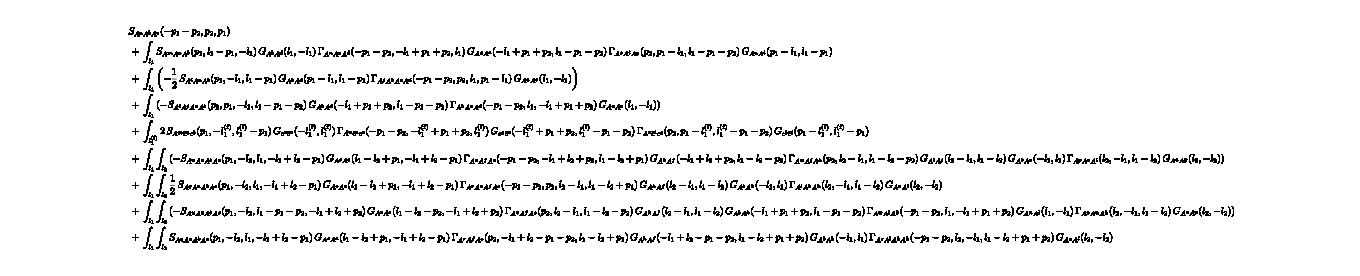

```mathematica
DSEA3=FTakeDerivatives[
FMakeDSE[Setup,A[i1]],{A[i3],A[i2]},
"Symmetries"->FMakeSymmetryList[{A[i1],A[i2],A[i3]}]
]//FTruncate//FPlot//FRoute//FPrint;
```

## 4Point

Or the four - gluon vertex :

```mathematica
DSEA4=FTakeDerivatives[
FMakeDSE[Setup,A[i1]],{A[i4],A[i3],A[i2]},
"Symmetries"->FMakeSymmetryList[{A[i1],A[i2],A[i3],A[i4]}]
]//FTruncate//FPlot//FRoute//FPrint;
```

-Graphics-+-Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

-Graphics-

## fRG

In the following, we list as examples also the fRG flow equations for the Yang-Mills setup we defined.

On a side - note, note that FTakeDerivatives automatically detects symmetries, e . g . for a three - point function:

```mathematica
fRGP3A=FTakeDerivatives[WetterichEquation,{A[i1],A[i2],A[i3]}];
```

In any FEx[...] you may add as an annotation a rule called “Symmetries”, which explains all possible permutations of external indices which affects the full diagram with a definite Factor (usually either 1 (symmetry) or -1 (antisymmetry)). FTakeDerivatives derives these symmetries always and annotates its result with them. Then, the diagrams are automatically simplified (i.e. identical ones can be identified) and put together, often considerably shortening the resulting expressions.
If you would like to turn off this behaviour, you can use FSetAutoBuildSymmetryList[False]

## 2-Point


-Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

-Graphics-

```mathematica
fRGAA=FTakeDerivatives[WetterichEquation,{A[i1],A[i2]}]//FTruncate//FPlot//FRoute//FPrint;
```

```mathematica
fRGcbc=FTakeDerivatives[WetterichEquation,{cb[i1],c[i2]}]//FTruncate//FPlot//FRoute//FPrint;
```

-Graphics--Graphics-+-Graphics--Graphics-

-Graphics-

## 3Point

```mathematica
fRGAcbc=FTakeDerivatives[WetterichEquation,{A[i1],cb[i2],c[i3]}]//FTruncate//FPlot//FRoute//FPrint;
```

-Graphics-+-Graphics-+-Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

-Graphics-

```mathematica
fRGA3=FTakeDerivatives[
WetterichEquation,{A[i1],A[i2],A[i3]},
"Symmetries"->FMakeSymmetryList[{A[i1],A[i2],A[i3]}]
]//FTruncate//FPlot//FRoute//FPrint;
```

-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

-Graphics-

## 4Point

```mathematica
fRGA4=FTakeDerivatives[
WetterichEquation,{A[i1],A[i2],A[i3],A[i4]},
"Symmetries"->FMakeSymmetryList[{A[i1],A[i2],A[i3],A[i4]}]
]//FTruncate//FPlot//FRoute//FPrint;
```

-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

-Graphics-